# lorentzian n cutoff

## fix σ; calculate <g|ρ|g> for ε = 10Ω; plot as a function of power of k

## parameters

```mathematica
α=1;
Ω=1;
ε=10 Ω;
```

```mathematica
numSteps=9;
nMin=1;nMax=10; nStepSize=Abs[nMin-nMax]/numSteps;
nValues=Table[n,{n,nMin,nMax,nStepSize}];
```

## smearing function

```mathematica
σ0=10^-4/Ω;
σ=σ0;
σNorm=σ/σ0;
```

```mathematica
f[x_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

## switching function

```mathematica
chiT1[t_]:=1/(r+T)1/2*(1+Cos[π/r(t+T/2)])
chiT2[t_]:=1/(r+T)
chiT3[t_]:=1/(r+T)1/2*(1+Cos[π/r(t-T/2)])
```

## k integrand

### the first interval

```mathematica
tpInt1[t_?NumericQ,k_?NumericQ]:=tpInt1[t,k]=NIntegrate[chiT1[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2-r,t}]
```

```mathematica
tInt1[k_?NumericQ]:=tInt1[k]=α*NIntegrate[chiT1[t] tpInt1[t,k],
{t,-T/2-r,-T/2}]
```

### the second interval

```mathematica
tpInt2[t_,k_]:=Integrate[chiT2[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2,t}]
```

```mathematica
tInt2[k_]:=α*Integrate[chiT2[t] tpInt2[t,k],
{t,-T/2,T/2}]
```

### the third interval

```mathematica
tpInt3[t_?NumericQ,k_?NumericQ]:=tpInt3[t,k]=NIntegrate[chiT3[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,T/2,t}]
```

```mathematica
tInt3[k_?NumericQ]:=tInt3[k]=α*NIntegrate[chiT3[t] tpInt3[t,k],
{t,T/2,T/2+r}]
```

this integrand with the transition from Abs[k] → k taken into account (i.e. can now properly integrate from 0 to ∞ with proper factor of 2)

```mathematica
kIntegrand[k_]:=-1/π*k*ftil[k]^2*(tInt1[k]+tInt2[k]+tInt3[k])
```

## cutoff function

```mathematica
lorNCutoff[k_,n_]:=ε^n/(Abs[k]^n+ε^n);
```

## <g|ρ|g>

```mathematica
T=2;r=0.2;
```

```mathematica
pLorN=Table[α+λ^2*NIntegrate[lorNCutoff[k,n]*kIntegrand[k],{k,0,∞}],{n,nMin,nMax,nStepSize}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.81037×10^7}. NIntegrate obtained -0.161996 and 0.000680694 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {255.}. NIntegrate obtained -0.1587 and 0.0000178699 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {255.}. NIntegrate obtained -0.156789 and 2.95144×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{1-0.161996 λ^2,1-0.1587 λ^2,1-0.156789 λ^2,1-0.155364 λ^2,1-0.154377 λ^2,1-0.153694 λ^2,1-0.153214 λ^2,1-0.152869 λ^2,1-0.152616 λ^2,1-0.152426 λ^2}

## plot

```mathematica
λ=0.1;Ω=.;
```

```mathematica
dataLorN=Transpose[{nValues,pLorN}];
```

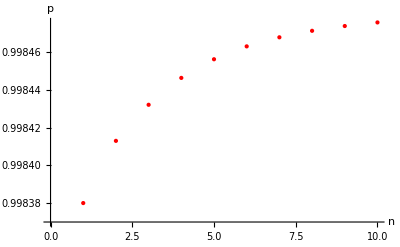

```mathematica
ListPlot[{dataLorN},
AxesLabel->{n,p},
PlotStyle->{Red},
PlotLabel->Style["",FontSize->16]]
```

## save the data!!

```mathematica
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pLorNvN.csv",dataLorN];
```